```mathematica
d1={{-2, -4}, {-1,15}, {0,-9},{1, 10},{2, 7},{3,6}}
```

{{-2,-4},{-1,15},{0,-9},{1,10},{2,7},{3,6}}

```mathematica
f1[x_]=a*x^2+b*x+c
```

c+b x+a x^2

```mathematica
Err1[a_,b_,c_]=Sum[(f1[d1[[i,1]]] - d1[[i,2]])^2,{i,1,Length[d1]}]
```

(9+c)^2+(4+4 a-2 b+c)^2+(-15+a-b+c)^2+(-10+a+b+c)^2+(-7+4 a+2 b+c)^2+(-6+9 a+3 b+c)^2

```mathematica
sol1=NSolve[{
D[Err1[a,b,c],a]==0,
D[Err1[a,b,c],b]==0,
D[Err1[a,b,c],c]==0
},{a,b,c}]
```

{{a→-0.285714,b→1.57143,c→4.28571}}

```mathematica
f1[x_]=f1[x]/.sol1[[1]]
```

4.28571+1.57143 x-0.285714 x^2

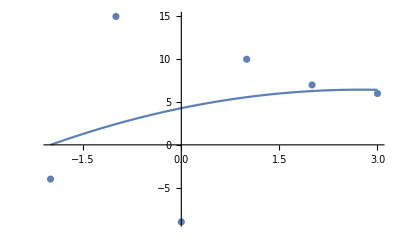

```mathematica
Show[ListPlot[d1], Plot[f1[x], {x, -2, 3}]]
```

```mathematica
d2={{1, 1},{2,2},{3,5},{4,9},{5,18},{6,34},{7,70},{8,132},{9,264},{10,537}}
```

{{1,1},{2,2},{3,5},{4,9},{5,18},{6,34},{7,70},{8,132},{9,264},{10,537}}

```mathematica
f2[x_]=a*E^(b*x)
```

a ⅇ^(b x)

```mathematica
Err2[c_,b_]=Sum[(Log[d2[[i,2]]] - (c + b *d2[[i,1]]))^2,{i,1,Length[d2]}]
```

(-b-c)^2+(-2 b-c+Log[2])^2+(-3 b-c+Log[5])^2+(-4 b-c+Log[9])^2+(-5 b-c+Log[18])^2+(-6 b-c+Log[34])^2+(-7 b-c+Log[70])^2+(-8 b-c+Log[132])^2+(-9 b-c+Log[264])^2+(-10 b-c+Log[537])^2

```mathematica
sol2=NSolve[{D[Err2[c,b],c]==0, D[Err2[c,b],b]==0},{c,b}]
```

{{c→-0.606029,b→0.690365}}

```mathematica
E^(-0.6060286058301532)
```

0.545513

```mathematica
f2[x_]=E^(-0.6060286058301532)*E^(b*x)/.sol2[[1]]
```

0.545513 ⅇ^(0.690365 x)

```mathematica
f3Py[x_]= 0.60658191 * E^(x * 0.67759405)
```

0.606582 ⅇ^(0.677594 x)

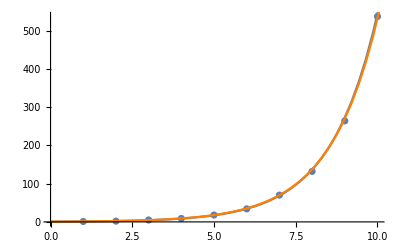

```mathematica
Show[ListPlot[d2],Plot[f2[x],{x, 0,11}], Plot[f3Py[x], {x, 0, 11}, PlotStyle->Orange]]
```

```mathematica
sumXiN[tuples_,n_]:=Sum[(tuples[[i,1]])^n,{i,Length[tuples]}]
X1={
{Length[d1], sumXiN[d1,1],sumXiN[d1,2]},
{sumXiN[d1,1],sumXiN[d1,2],sumXiN[d1,3]},
{sumXiN[d1,2],sumXiN[d1,3],sumXiN[d1,4]}
}
```

{{6,3,19},{3,19,27},{19,27,115}}

```mathematica
A1={a0,a1,a2}
```

{a0,a1,a2}

```mathematica
sumXiYiN[tuples_,n_]:=Sum[((tuples[[i,1]])^n) * tuples[[i,2]],{i,Length[tuples]}]
```

```mathematica
Y1={Sum[d1[[i,2]],{i,Length[d1]}], sumXiYiN[d1,1], sumXiYiN[d1,2]}
```

{25,35,91}

### X1*A1=Y1 -> A1=X1^(-1) . Y1

```mathematica
A1 = Inverse[X1].Y1//N
```

{4.28571,1.57143,-0.285714}

```mathematica
d3={{-3,7},{-2,4},{-1,-1},{0,1},{1,5},{2,6},{3,13}}
```

{{-3,7},{-2,4},{-1,-1},{0,1},{1,5},{2,6},{3,13}}

```mathematica
X3={
{Length[d3], sumXiN[d3,1],sumXiN[d3,2]},
{sumXiN[d3,1],sumXiN[d3,2],sumXiN[d3,3]},
{sumXiN[d3,2],sumXiN[d3,3],sumXiN[d3,4]}
}
```

{{7,0,28},{0,28,0},{28,0,196}}

```mathematica
Y3={Sum[d3[[i,2]],{i,Length[d3]}], sumXiYiN[d3,1], sumXiYiN[d3,2]}
```

{35,28,224}

```mathematica
A3=Inverse[X3].Y3
```

{1,1,1}

```mathematica
{1,1,1}.{1,x,x^2}
```

1+x+x^2

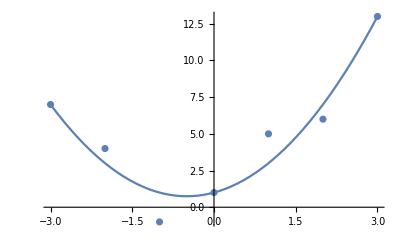

```mathematica
Show[ListPlot[d3],Plot[x^2+x+1,{x,-3,3}]]
```

```mathematica
nodes={{1,3},{4,10},{6,20},{8,30},{9,34},{11,40},{13,43}}
```

{{1,3},{4,10},{6,20},{8,30},{9,34},{11,40},{13,43}}

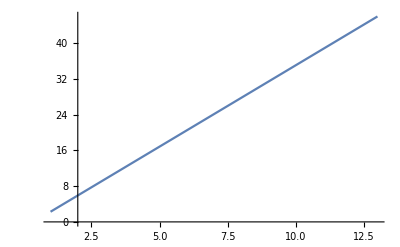

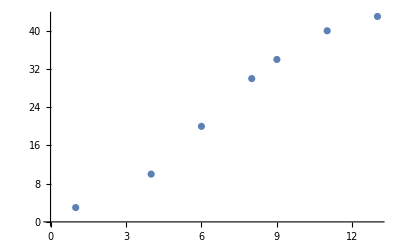

```mathematica
line = Plot[3.646067*x-1.370785,{x, 1, 13}]
dots = ListPlot[nodes]
```

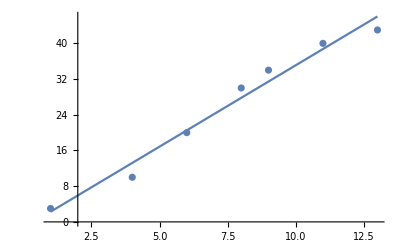

```mathematica
Show[line,dots]
```